{es→(3 √3)/500}

(3 √3)/500

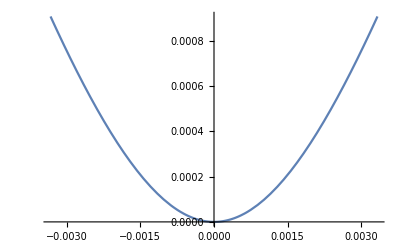

Solve::ivar: 3/1000 is not a valid variable.

Solve[False,3/1000]

```mathematica
(* ccd is 6.66 mm x 5.32 mm @ 5.2um square pixels *)
Clear[y,ho,phi,theta,es,z]
theta=60Degree;
phi = theta + Pi/2;
 z = 3*10^-3;
ho := z Sec[theta];
soln = Solve[y^2+(Sin[phi]^2-Cos[phi]^2 Tan[theta]^2)es^2-(2 ho Cos[phi] Tan[theta]^2)es == ho^2 Tan[theta]^2,es];
soln = soln[[2]];
y=0;
soln
4 z Sin[theta]
Plot[(es/.soln)- 4 z Sin[theta],{y,-3.33*10^-3,3.33*10^-3}] 
y = 3.33*10^-3;
Solve[(es/.soln)- 4 z Sin[theta]==46.3532*5.2*10^-6,z]
```

```mathematica
Clear[y,ho,phi,theta,es,z,c]
phi = theta + Pi/2;
ho := z Sec[theta];
soln = Solve[y^2+(Sin[phi]^2-Cos[phi]^2 Tan[theta]^2)es^2-(2 ho Cos[phi] Tan[theta]^2)es == ho^2 Tan[theta]^2,es];
soln = soln[[2]];
soln;
Solve[(es/.soln)- 4 z Sin[theta]==c,z]
```

```mathematica
{{z->},{z->(4 √2 √(c^2 Cos[theta]^4 Sin[theta]^2-6 y^2 Cos[theta]^4 Sin[theta]^2-4 y^2 Cos[theta]^5 Sin[theta]^2+c^2 Cos[theta]^4 Cos[2 theta] Sin[theta]^2-16 y^2 Cos[theta]^4 Cos[2 theta] Sin[theta]^2+4 y^2 Cos[theta]^4 Cos[3 theta] Sin[theta]^2-8 y^2 Cos[theta]^4 Cos[4 theta] Sin[theta]^2)-2 c Sin[2 theta]-4 c Sin[3 theta]+c Sin[4 theta]-4 c Sin[5 theta])/(4 (-1+2 Cos[theta]+3 Cos[2 theta]-3 Cos[3 theta]+Cos[5 theta]-2 Cos[6 theta]))}}
```